## First replicate Nakazawa by omitting ρ and setting f_i to published values

Define Model

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) -  aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (-aPR eP fP P+c0 (-1+eP+eΝ) r-aΝR (-1+eΝ) fΝ Ν)

-eP v (aPR (-1+eP) fP P-c0 (-1+eP+eΝ) r+aΝR eΝ fΝ Ν)

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1.,k-> 5., c0->0.25, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1., aΝR -> 1., bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1.};
kpars = Delete[pars, 2]
```

{r→1.,c0→0.25,fP→0.5,fΝ→0.5,aPR→0.25,aPΝ→1.,aΝR→1.,bPΝ→0.5,bΝR→0.5,bPR→0.5,mP→0.5,mΝ→0.5,v→1.}

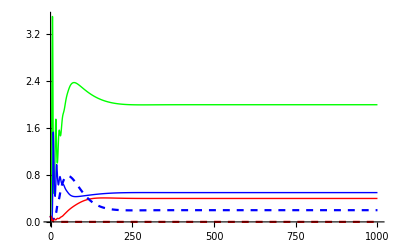

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.pars},{R,Ν, P, eΝ, eP},{t,0,1000}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,1000}, PlotStyle-> cols]
```

### Manipulate across gradients of k and aPΝ

```mathematica
(*Huzzah! Adaptive predator-specific model works! Not only do the stable/unstable and coexistence dynamics exactly match Nakazawa Fig. 3 but the effort variables  somehow (automatically) sum to less than 1 across all ranges of parameter space (something that I was worried about needing to constrain explicitely)*)
```

```mathematica
kaPΝpars = {r-> 1, c0->0.25, fP->0.5,fΝ->0.5,  aPR-> 0.25,aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1}
```

{r→1,c0→0.25,fP→0.5,fΝ→0.5,aPR→0.25,aΝR→1,bPΝ→0.5,bΝR→0.5,bPR→0.5,mP→0.5,mΝ→0.5,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[kaPΝpars,{k->κ,aPΝ->α}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{κ,5,"k"},0,20},{{α,1,"aPΝ"},0,4}]
```

Solve for equilibria and plot domains of coexistence

### Equilibria

```mathematica
equilRNP=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,deΝdt == 0,dPdt==0, dePdt==0},{R,Ν, eΝ,P, eP}]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
equil//TableForm
```

R→0 | Ν→0 | eΝ→1-eP | P→0 | 
R→-(-1+c0) k r | Ν→0 | eΝ→1-eP | P→0 | 
R→k r | Ν→0 | eΝ→0 | P→0 | eP→0
R→(k (aΝR (-1+fΝ) mP+aPR bPΝ mΝ-aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k) | Ν→(-aPR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (mP+aPR bPR (-1+c0) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eΝ→1 | P→(-aPΝ bPΝ mΝ+aΝR (-1+fΝ) k (-aΝR bΝR (-1+fΝ) mP-aPR bPR mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eP→0
R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aPR aΝR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ (aPΝ bPΝ c0+aPR aΝR (bPΝ bΝR c0+bPR (-c0+fΝ)) k) r)/(aPR aΝR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aPR aΝR bPR (-c0+fΝ) k r)/(aPR^2 aΝR bPR fΝ k) | eP→0
R→mP/(aPR bPR) | Ν→0 | eΝ→0 | P→(-mP/(bPR k)+aPR r)/aPR^2 | eP→0
R→0 | Ν→0 | eΝ→1 | P→0 | eP→0
R→-(-1+c0) k r | Ν→0 | eΝ→1 | P→0 | eP→0
R→mP/(aPR bPR) | Ν→0 | eΝ→1 | P→-(mP+aPR bPR (-1+c0) k r)/(aPR^2 bPR k) | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | eΝ→0 | P→(-mP+aPR bPR (-1+c0) (-1+fP) k r)/(aPR^2 bPR (-1+fP)^2 k) | eP→1
R→-(-1+c0) k r | Ν→0 | eΝ→1-1/fP+mP/(aPR bPR fP k r-aPR bPR c0 fP k r) | P→0 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→((-c0+fP) k r)/fP | Ν→0 | eΝ→0 | P→(c0 r)/(aPR fP) | eP→1/fP+mP/(aPR bPR c0 k r-aPR bPR fP k r)
R→(1-(c0 (fP+fΝ))/(fP fΝ)) k r | Ν→(c0 r)/(aΝR fΝ) | eΝ→(aPR fP fΝ mΝ+aPΝ c0 fΝ r+aPR aΝR bΝR (-fP fΝ+c0 (fP+fΝ)) k r)/(aPR aΝR bΝR fΝ (-fP fΝ+c0 (fP+fΝ)) k r) | P→(c0 r)/(aPR fP) | eP→(aΝR fP fΝ mP-aPΝ bPΝ c0 fP r+aPR aΝR bPR (-fP fΝ+c0 (fP+fΝ)) k r)/(aPR aΝR bPR fP (-fP fΝ+c0 (fP+fΝ)) k r)
R→(k (aΝR bΝR fΝ (fP+fΝ-fP fΝ) mP+aPR bPR fP (fP+fΝ-fP fΝ) mΝ-aPΝ (bPR-bPΝ bΝR) (-1+c0) fP fΝ r))/(aPΝ (bPR-bPΝ bΝR) fP fΝ+aPR aΝR bPR bΝR (fP+fΝ-fP fΝ)^2 k) | Ν→(-fP (aΝR bΝR fΝ mP+aPR bPR fP mΝ)+aPR aΝR bPR bΝR (-1+c0) fP (fP (-1+fΝ)-fΝ) k r)/(aΝR (aPΝ (bPR-bPΝ bΝR) fP fΝ+aPR aΝR bPR bΝR (fP+fΝ-fP fΝ)^2 k)) | eΝ→(aPR aΝR (fP (-1+fΝ)-fΝ) k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ)-aPΝ (aΝR fΝ mP+aPR bPΝ fP mΝ)-aPR aPΝ aΝR (-1+c0) (bPΝ bΝR fP-bPR (-1+fP) fΝ) k r)/(aPR aΝR k ((fP (-1+fΝ)-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)+aPΝ (bPR-bPΝ bΝR) (-1+c0) fP fΝ r)) | P→-(fΝ (aPR bPR fP mΝ+aΝR bΝR (fΝ mP-aPR bPR (-1+c0) (fP (-1+fΝ)-fΝ) k r)))/(aPR (aPΝ (bPR-bPΝ bΝR) fP fΝ+aPR aΝR bPR bΝR (fP+fΝ-fP fΝ)^2 k)) | eP→(aPR aΝR (fP (-1+fΝ)-fΝ) k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (aΝR fΝ mP+aPR bPΝ fP mΝ-aPR aΝR (-1+c0) (bPΝ bΝR fP (-1+fΝ)-bPR fΝ) k r))/(aPR aΝR k ((fP (-1+fΝ)-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)+aPΝ (bPR-bPΝ bΝR) (-1+c0) fP fΝ r))
R→-(k (aΝR mP+aPR bPΝ (-1+fP) mΝ+aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k) | Ν→(-aPR (-1+fP) k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ)+aPΝ (mP+aPR bPR (-1+c0+fP-c0 fP) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | eΝ→0 | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | eP→1
R→(aPR fP mΝ+aPΝ c0 r)/(aPR aΝR bΝR fP) | Ν→(-aPR fP mΝ-aPΝ c0 r+aPR aΝR bΝR (-c0+fP) k r)/(aPR aΝR^2 bΝR fP k) | eΝ→0 | P→(c0 r)/(aPR fP) | eP→(aPR fP (-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ))+aPΝ (-aPΝ bPΝ c0+aPR aΝR (bPR c0+bPΝ bΝR (-c0+fP)) k) r)/(aPR aΝR bPR fP k (aPR fP mΝ+aPΝ c0 r))
R→mΝ/(aΝR bΝR) | Ν→(-mΝ/(bΝR k)+aΝR r)/aΝR^2 | eΝ→0 | P→0 | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→1
R→-(-1+c0) k r | Ν→0 | eΝ→0 | P→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(mΝ+aΝR bΝR (-1+c0) k r)/(aΝR^2 bΝR k) | eΝ→0 | P→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r)/(aΝR^2 bΝR (-1+fΝ)^2 k) | eΝ→1 | P→0 | eP→0
R→-(-1+c0) k r | Ν→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | P→0 | eP→1-1/fΝ+mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)
R→((-c0+fΝ) k r)/fΝ | Ν→(c0 r)/(aΝR fΝ) | eΝ→1/fΝ+mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r) | P→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→1 | P→-mΝ/aPΝ | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→0 | P→-mΝ/aPΝ | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→0 | P→-mΝ/aPΝ | eP→1
R→(k (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eΝ→0 | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→0

```mathematica
FullSimplify[equil[[17, 2,  2]]]
```

(-mΝ/(bΝR k)+aΝR r)/aΝR^2

```mathematica
equil/.kpars//TableForm
```

Power::infy: Infinite expression 1/0. encountered.

R→0 | Ν→0 | eΝ→1-eP | P→0 | 
R→0.75 k | Ν→0 | eΝ→1-eP | P→0 | 
R→1. k | Ν→0 | eΝ→0 | P→0 | eP→0
R→(0.1875 k)/(0.5-0.03125 k) | Ν→(1. (1. (0.5-0.09375 k)+0.015625 k))/(0.5-0.03125 k) | eΝ→1 | P→(1. (-0.25+0.0625 k))/(0.5-0.03125 k) | eP→0
R→2. | Ν→0.5 | eΝ→(128. (-1. (0.125+0.046875 k)+0.5 (0.5+0.046875 k)))/k | P→(64. (-0.125+0.03125 k))/k | eP→0
R→4. | Ν→0 | eΝ→0 | P→16. (0.25-1./k) | eP→0
R→0 | Ν→0 | eΝ→1 | P→0 | eP→0
R→0.75 k | Ν→0 | eΝ→1 | P→0 | eP→0
R→4. | Ν→0 | eΝ→1 | P→-(32. (0.5-0.09375 k))/k | eP→0
R→8. | Ν→0 | eΝ→0 | P→(128. (-0.5+0.046875 k))/k | eP→1
R→0.75 k | Ν→0 | eΝ→-1.+10.6667/k | P→0 | eP→2. (1-5.33333/k)
R→0.5 k | Ν→0 | eΝ→0 | P→2. | eP→2.-16./k
R→0. | Ν→0.5 | eΝ→ComplexInfinity | P→2. | eP→ComplexInfinity
R→(0.164063 k)/(0.0625+0.0351563 k) | Ν→(1. (-0.078125+0.0175781 k))/(0.0625+0.0351563 k) | eΝ→-(24.381 (-0.28125+0.00585938 k))/k | P→-(2. (0.03125+0.5 (0.25-0.0703125 k)))/(0.0625+0.0351563 k) | eP→-(24.381 (1. (0.28125-0.0585938 k)+0.0117188 k))/k
R→-(0.09375 k)/(0.5-0.03125 k) | Ν→(1. (1. (0.5-0.046875 k)+0.0273438 k))/(0.5-0.03125 k) | eΝ→0 | P→-(1. (0.25+0.03125 k))/(0.5-0.03125 k) | eP→1
R→5. | Ν→(16. (-0.3125+0.03125 k))/k | eΝ→0 | P→2. | eP→(51.2 (0.125 (-0.25-0.1875 k)+1. (-0.125+0.046875 k)))/k
R→1. | Ν→1. (1.-1./k) | eΝ→0 | P→0 | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→1
R→0.75 k | Ν→0 | eΝ→0 | P→0 | eP→1
R→1. | Ν→-(2. (0.5-0.375 k))/k | eΝ→0 | P→0 | eP→1
R→2. | Ν→(8. (-0.5+0.1875 k))/k | eΝ→1 | P→0 | eP→0
R→0.75 k | Ν→0 | eΝ→2. (1-1.33333/k) | P→0 | eP→-1.+2.66667/k
R→0.5 k | Ν→0.5 | eΝ→2.-4./k | P→0 | eP→0
R→0 | Ν→1. | eΝ→1 | P→-0.5 | eP→0
R→0 | Ν→1. | eΝ→0 | P→-0.5 | eP→0
R→0 | Ν→1. | eΝ→0 | P→-0.5 | eP→1
R→(0.0625 k)/(0.5-0.0625 k) | Ν→(1. (1. (0.5-0.125 k)+0.046875 k))/(0.5-0.0625 k) | eΝ→0 | P→(1. (-0.25+0.0625 k))/(0.5-0.0625 k) | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→0

```mathematica
ex = equil[[23, 3, 2]];
Solve[ex==0, k]
```

{{k→(fΝ mΝ)/(aΝR bΝR (-c0+fΝ) r)}}

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν) | aPR (-1+eP fP) R | (aPR fP P-c0 r) R
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν | -aPΝ Ν | 0
0 | -aΝR (-1+eΝ) eΝ fΝ v | v (-aPR eP fP P+c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fΝ Ν) | -aPR eP eΝ fP v | eΝ (-aPR fP P+c0 r) v
aPR bPR (1-eP fP) P | aPΝ bPΝ P | 0 | -mP+aPR bPR (1-eP fP) R+aPΝ bPΝ Ν | -aPR bPR fP P R
0 | -aΝR eP eΝ fΝ v | eP v (c0 r-aΝR fΝ Ν) | -aPR (-1+eP) eP fP v | v (aPR (1-2 eP) fP P+c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν))

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν)
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν
0 | -aΝR (-1+eΝ) eΝ fΝ v | v (-aPR eP fP P+c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fΝ Ν))

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aPR (-1+eP fP) R | (aPR fP P-c0 r) R
aPR bPR (1-eP fP) P | -mP+aPR bPR (1-eP fP) R+aPΝ bPΝ Ν | -aPR bPR fP P R
0 | -aPR (-1+eP) eP fP v | v (aPR (1-2 eP) fP P+c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν))

```mathematica
mat = JRΝ/.equil[[17,All]]//FullSimplify;
```

```mathematica
mat//MatrixForm
```

(-mΝ/(aΝR bΝR k) | -mΝ/bΝR | (mΝ (-fΝ mΝ+aΝR bΝR (-c0+fΝ) k r))/(aΝR^2 bΝR^2 k)
-mΝ/(aΝR k)+bΝR r | 0 | (fΝ mΝ (mΝ-aΝR bΝR k r))/(aΝR^2 bΝR k)
0 | 0 | (-(fΝ mΝ)/(aΝR bΝR k)+(-c0+fΝ) r) v)

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[pars,2];
```

```mathematica
(* function to substitute equilibrium densities of a given equilibrium into Jacobian. Works. *)
```

```mathematica
Jeq3=J/.equil[[3,All]]//FullSimplify;
Jeq4=J/.equil[[4,All]]//FullSimplify;
Jeq5=J/.equil[[5,All]]//FullSimplify;
Jeq6=J/.equil[[6,All]]//FullSimplify;
Jeq10=J/.equil[[10,All]]//FullSimplify;
Jeq12=J/.equil[[12,All]]//FullSimplify;
Jeq17=J/.equil[[17,All]]//FullSimplify;
Jeq21=J/.equil[[21,All]]//FullSimplify;
Jeq23=J/.equil[[23,All]]//FullSimplify;
Jeq27=J/.equil[[27,All]]//FullSimplify;
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq23RΝ=JRΝ/.equil[[23,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq12RP=JRP/.equil[[12,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
```

```mathematica
(* function to test if all abundances are greater than zero;used for region of feasibility. For plotting purposes, provides the region of "existence" but not "stability"*)
```

```mathematica
AllFeas3[k_]=AllTrue[Re[equil[[3,All,2]]/.kpars],#≥0&];
AllFeas4[k_]=AllTrue[Re[equil[[4,All,2]]/.kpars],#≥0&];
AllFeas5[k_]=AllTrue[Re[equil[[5,All,2]]/.kpars],#≥0&];
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.kpars],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.kpars],#≥0&];
AllFeas12[k_]=AllTrue[Re[equil[[12,All,2]]/.kpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.kpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.kpars],#≥0&];
AllFeas23[k_]=AllTrue[Re[equil[[23,All,2]]/.kpars],#≥0&];
AllFeas27[k_]=AllTrue[Re[equil[[27,All,2]]/.kpars],#≥0&];
```

```mathematica
AllFeas23[4.5]
```

True

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
pReEig3[k_]=Max[Re[Eigenvalues[N[Jeq3/.kpars], 3]]];
pReEig4[k_]=Max[Re[Eigenvalues[N[Jeq4/.kpars], 3]]];
pReEig5[k_]=Max[Re[Eigenvalues[N[Jeq5/.kpars], 3]]];
pReEig6[k_]=Max[Re[Eigenvalues[N[Jeq6/.kpars], 3]]];
pReEig10[k_]=Max[Re[Eigenvalues[N[Jeq10/.kpars],3]]];
pReEig12[k_]=Max[Re[Eigenvalues[N[Jeq12/.kpars],3]]];
pReEig17[k_]=Max[Re[Eigenvalues[N[Jeq17/.kpars],3]]];
pReEig21[k_]=Max[Re[Eigenvalues[N[Jeq21/.kpars], 3]]];
pReEig23[k_]=Max[Re[Eigenvalues[N[Jeq23/.kpars], 3]]];
pReEig27[k_]=Max[Re[Eigenvalues[N[Jeq27/.kpars], 3]]];
```

```mathematica
(*R system*)
```

```mathematica
pReEig3R[k_]=Max[Re[Eigenvalues[N[Jeq3/.kpars], 1]]];
```

```mathematica
(* RN system *)
```

```mathematica
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.kpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.kpars]]]];
pReEig23RΝ[k_]=Max[Re[Eigenvalues[N[Jeq23RΝ/.kpars]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.kpars]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.kpars]]]];
pReEig12RP[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.kpars]]]];
```

Produce plots

### Abundance-gradient plots (MN)

#### Across k

```mathematica
(* Functions for species-specific equilibria. Gives value of resource for a given k (and IGP strength) at each euilibrium (which can be specified using the double-brackets) *)
pEquilR[k_]=equil[[All,1,2]]/.kpars//FullSimplify
pEquilΝ[k_]=equil[[All,2,2]]/.kpars//FullSimplify;
pEquilP[k_]=equil[[All,4,2]]/.kpars//FullSimplify;
pEquileΝ[k_]=equil[[All,3,2]]/.kpars//FullSimplify;
pEquileP[k_]=equil[[All,5,2]]/.kpars//FullSimplify;
```

{0,0.75 k,1. k,-(6. k)/(-16.+1. k),2.,4.,0,0.75 k,4.,8.,0.75 k,0.5 k,0.,(4.66667 k)/(1.77778+1. k),(3. k)/(-16.+1. k),5.,1.,0,0.75 k,1.,2.,0.75 k,0.5 k,0,0,0,-(1. k)/(-8.+1. k),0}

Power::infy: Infinite expression 1/0. encountered.

Part::partw: Part 5 of {R→0,Ν→0,eΝ→1-eP,P→0} does not exist.

Power::infy: Infinite expression 1/0. encountered.

Part::partw: Part 5 of {R→0,Ν→0,eΝ→1-eP,P→0} does not exist.

#### R-RN system

```mathematica
(* Resource *)
```

```mathematica
ELineCols={
{Thin,Green},{Thick,Dashed, Green},{Thin, Blue},{Thick, Dashed,Blue},{Thin,Opacity[0.5, Blue]},{Thick, Dashed,Opacity[0.5, Blue]},
{Thin,Red},{Thick,Dashed,Red}, {Thin,Opacity[0.5, Red]},{Thick,Dashed,Opacity[0.5, Red]}};
```

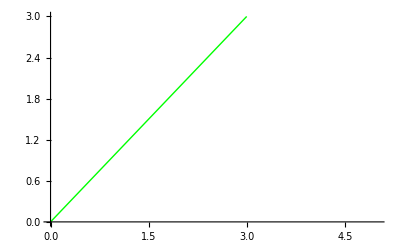

-Graphics-

```mathematica
PlotEqR3=Plot[{pEquilR[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,3}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0&&AllFeas3[x]]]
PlotEqR3u=Plot[{pEquilR[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,3}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥0&&AllFeas3[x]]]
```

```mathematica
PlotEqR17=Plot[{pEquilR[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];
PlotEqR17u=Plot[{pEquilR[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
```

```mathematica
PlotEqR21=Plot[{pEquilR[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];
PlotEqR21u=Plot[{pEquilR[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig21RΝ[x]≥   0&&AllFeas21[x]]];
(*FiguRed out why things get scRewy with this equilibRium--the max Real eigenvalues is 0. acRoss the entiRe Range of existence. I think this means that it is veRy neaRy zeRo the whole way but makes the exact tRansition at k=4.  We only disceRn this by doing the math of the chaRacteRistic equation*)
```

```mathematica
PlotEqR23=Plot[{pEquilR[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]<0&&AllFeas23[x]]];
PlotEqR23u=Plot[{pEquilR[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig23RΝ[x]≥0&&AllFeas23[x]]];
```

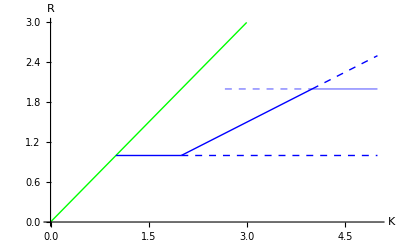

```mathematica
Show[PlotEqR3,PlotEqR3u,  PlotEqR17,PlotEqR17u,  PlotEqR21,PlotEqR21u,  PlotEqR23,PlotEqR23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

```mathematica
(* Intermediate consumer *)
```

```mathematica
PlotEqΝ3=Plot[{pEquilΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0.&&AllFeas3[x]]];
PlotEqΝ3u=Plot[{pEquilΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥ 0.&&AllFeas3[x]]];
PlotEqΝ17=Plot[{pEquilΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0.&&AllFeas17[x]]];
PlotEqΝ17u=Plot[{pEquilΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0.&&AllFeas17[x]]];
PlotEqΝ21=Plot[{pEquilΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0.&&AllFeas21[x]]];
PlotEqΝ21u=Plot[{pEquilΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0.&&AllFeas21[x]]];
PlotEqΝ23=Plot[{pEquilΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]< 0.&&AllFeas23[x]]];
PlotEqΝ23u=Plot[{pEquilΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig23RΝ[x]≥0.&&AllFeas23[x]]];
```

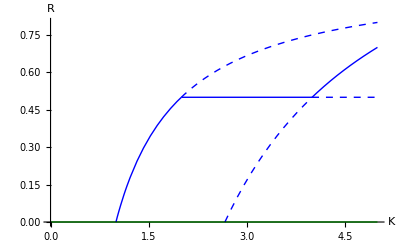

```mathematica
Show[PlotEqΝ3,PlotEqΝ3u,  PlotEqΝ17,PlotEqΝ17u,  PlotEqΝ21,PlotEqΝ21u,  PlotEqΝ23,PlotEqΝ23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

```mathematica
(* Level of efense against the intermediate consumer *)
```

```mathematica
PlotEqeΝ3=Plot[{pEquileΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<   0&&AllFeas3[x]]];
PlotEqeΝ3u=Plot[{pEquileΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥ 0&&AllFeas3[x]]];
PlotEqeΝ17=Plot[{pEquileΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0&&AllFeas17[x]]];
PlotEqeΝ17u=Plot[{pEquileΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
PlotEqeΝ21=Plot[{pEquileΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0&&AllFeas21[x]]];
PlotEqeΝ21u=Plot[{pEquileΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0&&AllFeas21[x]]];
PlotEqeΝ23=Plot[{pEquileΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]< 0&&AllFeas23[x]]];
PlotEqeΝ23u=Plot[{pEquileΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig23RΝ[x]≥0&&AllFeas23[x]]];
```

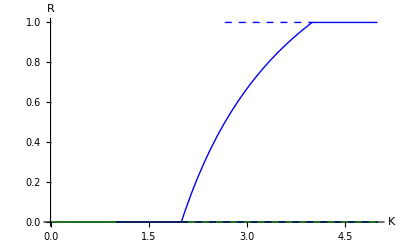

```mathematica
Show[PlotEqeΝ3,PlotEqeΝ3u,  PlotEqeΝ17,PlotEqeΝ17u,  PlotEqeΝ21,PlotEqeΝ21u,  PlotEqeΝ23,PlotEqeΝ23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

#### R-RN-RNP-RP

### Invasibility plot (Fig 2.)

#### One equilibrium at a time

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN23 = equil[[23,1,2]];
NstarRN23= equil[[23,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
PinvRN23 = bPR aPR (1 -0*fP)RstarRN23  + aPN bPΝ NstarRN23 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝpars
PlotRN17 = Plot[PinvRN17kaPN,{k, 1,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN23 = FullSimplify[Solve[PinvRN23==0,aPN]][[1,1,2]];
PinvRN23kaPN = plotPinvRN23/.kaPΝpars;
PlotRN23 = Plot[PinvRN23kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig23RΝ[x]<0&&AllFeas23[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝpars;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];
```

-(0.375 k)/(0.5-0.5 k)

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,4,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,4,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,4,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝpars;
PlotRP6 = Plot[Νinv6kaPN,{k, 4,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.kaPΝpars;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝpars;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

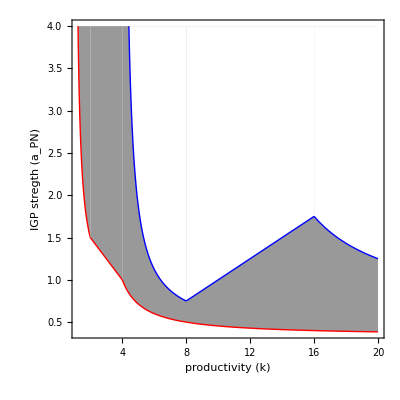

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN17, PlotRN21,PlotRN23,PlotRP6,PlotRP10, PlotRP12, PlotRange->Automatic, Frame->True,FrameLabel->{"productivity (k)","IGP stregth (a_PN)"}, AspectRatio -> 1/1, LabelStyle -> Larger]
```